```mathematica
n=300;
```

```mathematica
z=1.96;
(* This is the plot of the normal approximation interval and the Wilson score interval *)
```

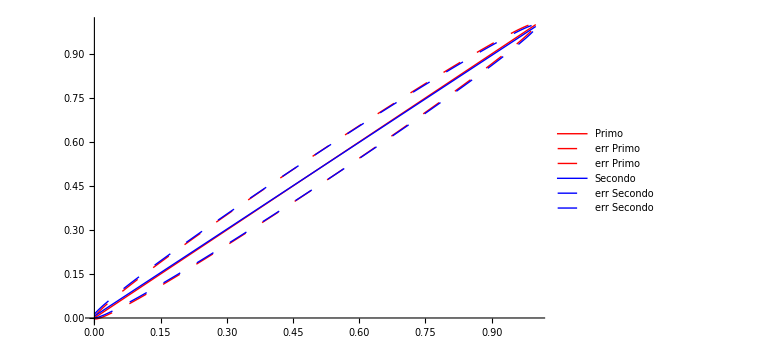

```mathematica
Plot[{p,p+z*Sqrt[(1/n)*p*(1-p)],p-z*Sqrt[(1/n)*p*(1-p)],(p+(z^2)/(2*n))/(1+(z^2)/n),(p+(z^2)/(2*n))/(1+(z^2)/n)+(z*Sqrt[p*(1-p)/n+(z^2)/(4*(n^2))])/(1+(z^2)/n),(p+(z^2)/(2*n))/(1+(z^2)/n)-(z*Sqrt[p*(1-p)/n+(z^2)/(4*(n^2))])/(1+(z^2)/n)},{p,0,1},PlotStyle->{{Red,Dashing[None]},{Red,Dashing[Large]},{Red,Dashing[Large]},{Blue,Dashing[None]},{Blue,Dashing[Large]},{Blue,Dashing[Large]}},PlotLegends->{Primo,Primo err,Primo err, Secondo, Secondo err, Secondo err},ImageSize->Large]
```

```mathematica
(* This is the plot of the differences between the normal approximation interval and the Wilson score interval for p and the error *)
```

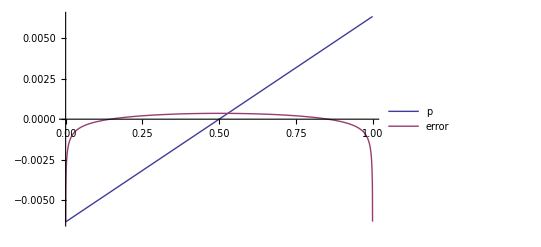

```mathematica
Plot[{p-(p+(z^2)/(2*n))/(1+(z^2)/n),z*Sqrt[(1/n)*p*(1-p)]-(z*Sqrt[p*(1-p)/n+(z^2)/(4*(n^2))])/(1+(z^2)/n)},{p,0,1},PlotLegends->{p,error}]
```